Rechnung zu einem einzelnen Soliton


Rechnung für Variationen der effektiven Geschwindigkeit

```mathematica
(*Parameter definieren*)
Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)
l=1; (*ϵ - Terme*)


mMax=2;
vmValues={v1,v2,v3,v4,v5,v6,v7,v8,v9,v10}; (*v_ef- Terme*)
θVerschiebung=θVerschiebung;


dim=2*Ntrunc+1;
Mv=ConstantArray[0,{dim,dim}];

Do[n=k-Ntrunc-1;
(*Diagonalelement:a_{n}*)
Mv[[k,k]]=-v0*n/2*(-1)^n;
(*Off-Diagonale:a_{n+l} *)
indexPlusL=k+l;
If[1<=indexPlusL<=dim,Mv[[k,indexPlusL]]=ϵ0/2];
(*Off-Diagonale:a_{n-l}*)
indexMinusL=k-l;
If[1<=indexMinusL<=dim,Mv[[k,indexMinusL]]=ϵ0/2  ];


For[m=1,m<=Length[vmValues],m++, (*zählt die verschiedenen frequenzen durch von v_eff ab v_1*)
(*Off-Diagonale:a_{n+m} *)
indexPlusM=k+m;
If[1<=indexPlusM<=dim,Mv[[k,indexPlusM]]+=-1/4 (-1)^(n+m) (n+m+m/2) vmValues[[m]]*Exp[I*m/2 * θVerschiebung]];
(*Off-Diagonale:a_{n-m} *)
indexMinusM=k-m;
If[1<=indexMinusM<=dim,Mv[[k,indexMinusM]]+=-1/4 (-1)^(n-m) (n-m-m/2) vmValues[[m]]*Exp[I*m/2 * θVerschiebung]];
],
{k,1,dim}

] 


Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
MatrixForm[Mv];
```

Matrix M erstellt. Dimension: 801x801

Test 1

{1,2,3,4,5,6,7,8,9,10}

{0.,0.0225 (ⅇ^(-ⅈ ϕ)+ⅇ^(ⅈ ϕ)),0.,0.,0.,0.,0.,0.,0.,0.}

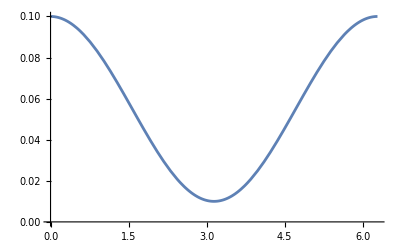

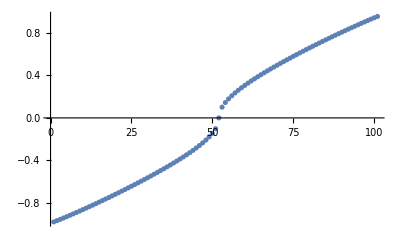

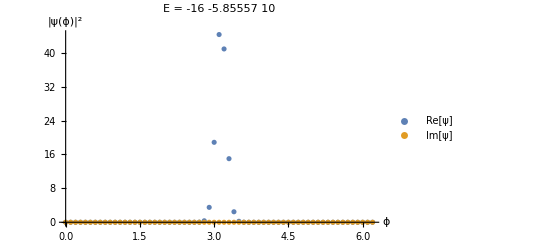

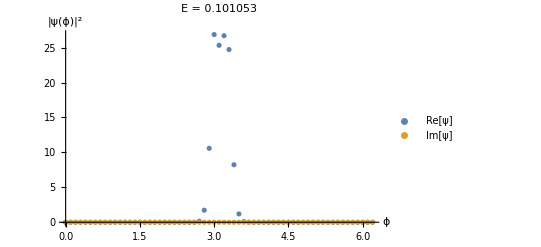

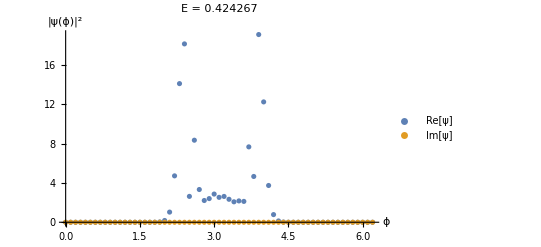

```mathematica
ϵvValues={1,0.055,0,0.045,0,0,0,0,0,0,0,0};
θVerschiebung=0;

v0Test=ϵvValues[[2]];
lValues=Range[1,Length[ϵvValues[[3;;]]]]
vlTest=0.5*ϵvValues[[3;;]]*(Exp[I*lValues/2 * ϕ]+Exp[-I*lValues/2 * ϕ])*Exp[I*lValues/2 * θVerschiebung]
Plot[Re[v0Test+Total[vlTest]],{ϕ,0,2 Pi},PlotRange->{Automatic,{0,Automatic}}]



{vals,vecs}=Eigensystem[Mv/.Thread[{ϵ0,v0,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10}->ϵvValues]];
ListPlot[Sort[Re[vals]][[350;;450]]]



{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{Re[vals],vecs}],First]];
positionsv={401,402,415};(*{100,380,393,395,399,401,403,407,409,422,702};*)

For[i=1,i<=Length[positionsv],i++,
pos=positionsv[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1v=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2v=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψv=Conjugate[{ψ1v,ψ2v}].{ψ1v,ψ2v};
Print[ListPlot[{
Table[{ϕ,Re[ψv]},{ϕ,0,2Pi,0.1}],
Table[{ϕ,Im[ψv]},{ϕ,0,2Pi,0.1}]},
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLegends->{"Re[ψ]","Im[ψ]"},PlotLabel->"E = "<>ToString[sortedNeigvalsSingle[[pos]]]]]
]
```

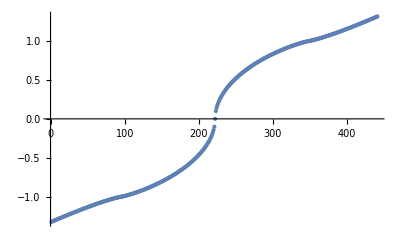

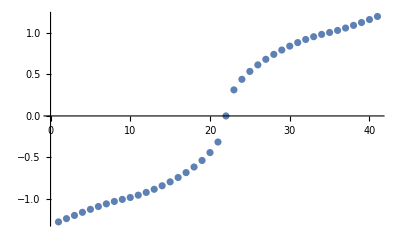

Test 2

{1,2,3,4,5,6,7,8,9,10}

{0.+0. ⅈ,0.0200185 (ⅇ^(-ⅈ ϕ)+ⅇ^(ⅈ ϕ)),0.+0. ⅈ,-0.0102778 (ⅇ^(-2 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ)),0.+0. ⅈ,0.00338338 (ⅇ^(-3 ⅈ ϕ)+ⅇ^(3 ⅈ ϕ)),0.+0. ⅈ,-0.00071414 (ⅇ^(-4 ⅈ ϕ)+ⅇ^(4 ⅈ ϕ)),0.+0. ⅈ,0.000096648 (ⅇ^(-5 ⅈ ϕ)+ⅇ^(5 ⅈ ϕ))}

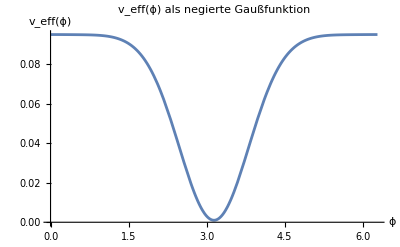

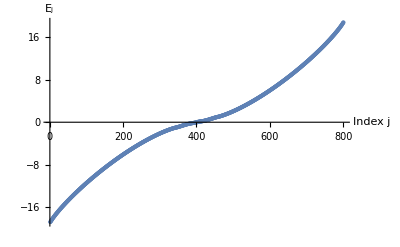

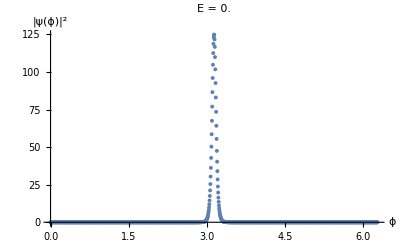

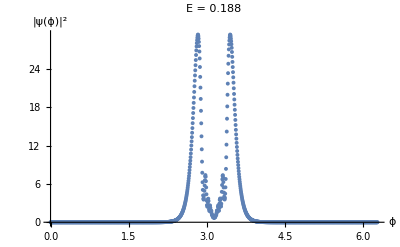

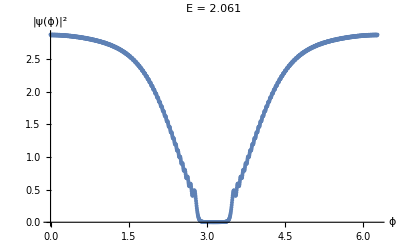

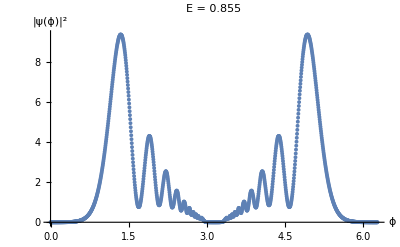

```mathematica
ϵvValues={1,0.07,0,-0.0400369,0,-0.0205556,0,-0.00676676,0,-0.00142828,0,-0.000193296};
θVerschiebung=Pi;

v0Test=ϵvValues[[2]];
lValues=Range[1,Length[ϵvValues[[3;;]]]]
vlTest=0.5*ϵvValues[[3;;]]*(Exp[I*lValues/2 * ϕ]+Exp[-I*lValues/2 * ϕ])*Exp[I*lValues/2 * θVerschiebung]
Plot[Re[v0Test+Total[vlTest]],{ϕ,0,2 Pi},
PlotRange->{Automatic,{0,Automatic}}, PlotLabel->"v_eff(ϕ) als negierte Gaußfunktion",AxesLabel->{"ϕ","v_eff(ϕ)"}]



{vals,vecs}=Eigensystem[Mv/.Thread[{ϵ0,v0,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10}->ϵvValues]];
ListPlot[Sort[Re[vals]],AxesLabel->{"Index j","E_j"}]


PlotsvGauss01={};
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{Re[vals],vecs}],First]];
positionsv={401,415,450,500};(*{100,380,393,395,399,401,403,407,409,422,702};*)

For[i=1,i<=Length[positionsv],i++,
pos=positionsv[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1v=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2v=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψv=Conjugate[{ψ1v,ψ2v}].{ψ1v,ψ2v};
plot=ListPlot[
Table[{ϕ,Re[ψv]},{ϕ,0,2Pi,0.005}],
Ticks->{Automatic,None},
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]],PlotMarkers->{Automatic, Tiny}];
AppendTo[PlotsvGauss01,plot]
Print[plot]
]
(*GraphicsRow[PlotsvGauss01,ImageSize->Full]*)
```

Test 3

0

{1,2,3,4,5,6,7,8,9,10}

{0.,0.1 (ⅇ^(-ⅈ ϕ)+ⅇ^(ⅈ ϕ)),0.,0.1 (ⅇ^(-2 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ)),0.,0.,0.,0.,0.,0.}

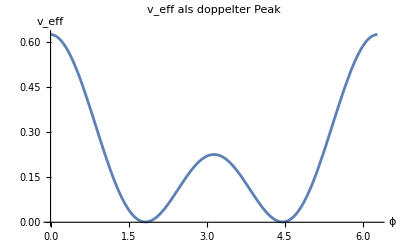

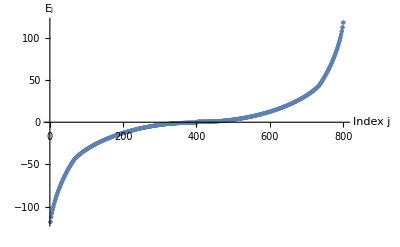

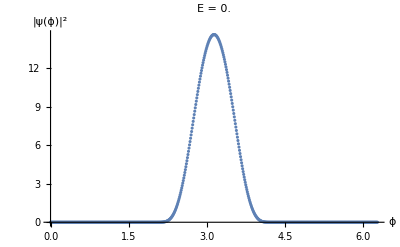

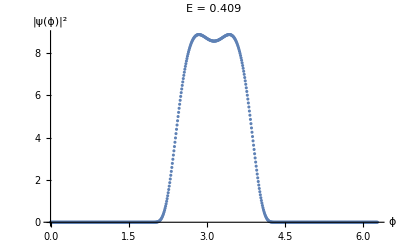

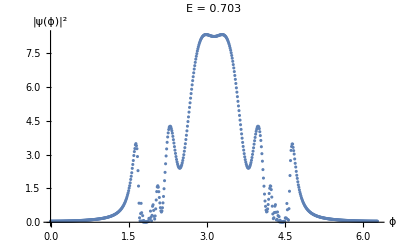

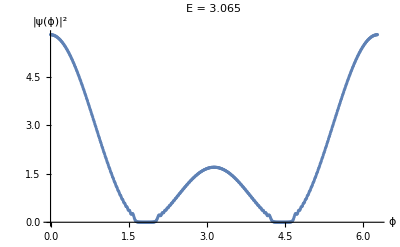

```mathematica
ϵvValues={1,0.226,0,0.2,0,0.2,0,0,0,0,0,0};
θVerschiebung=0

v0Test=ϵvValues[[2]];
lValues=Range[1,Length[ϵvValues[[3;;]]]]
vlTest=0.5*ϵvValues[[3;;]]*(Exp[I*lValues/2 * ϕ]+Exp[-I*lValues/2 * ϕ])*Exp[I*lValues/2 * θVerschiebung]
Plot[Re[v0Test+Total[vlTest]],{ϕ,0,2 Pi},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"v_eff als doppelter Peak",AxesLabel->{"ϕ","v_eff"}]



{vals,vecs}=Eigensystem[Mv/.Thread[{ϵ0,v0,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10}->ϵvValues]];
ListPlot[Sort[Re[vals]],AxesLabel->{"Index j","E_j"}]


PlotsvGauss02={};
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{Re[vals],vecs}],First]];
positionsv={401,402,430,500};(*{100,380,393,395,399,401,403,407,409,422,702};*)

For[i=1,i<=Length[positionsv],i++,
pos=positionsv[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1v=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2v=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψv=Conjugate[{ψ1v,ψ2v}].{ψ1v,ψ2v};
plot=ListPlot[
Table[{ϕ,Re[ψv]},{ϕ,0,2Pi,0.01}],
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]];
AppendTo[PlotsvGauss02,plot]
Print[plot]
]
(*GraphicsRow[PlotsvGauss02,ImageSize->Full]*)
```

```mathematica
Test 4
```

{1,2,3,4,5,6,7,8,9,10}

{0.+0. ⅈ,-0.0200185 (ⅇ^(-ⅈ ϕ)+ⅇ^(ⅈ ϕ)),0.+0. ⅈ,0.0102778 (ⅇ^(-2 ⅈ ϕ)+ⅇ^(2 ⅈ ϕ)),0.+0. ⅈ,-0.00338338 (ⅇ^(-3 ⅈ ϕ)+ⅇ^(3 ⅈ ϕ)),0.+0. ⅈ,0.00071414 (ⅇ^(-4 ⅈ ϕ)+ⅇ^(4 ⅈ ϕ)),0.+0. ⅈ,-0.000096648 (ⅇ^(-5 ⅈ ϕ)+ⅇ^(5 ⅈ ϕ))}

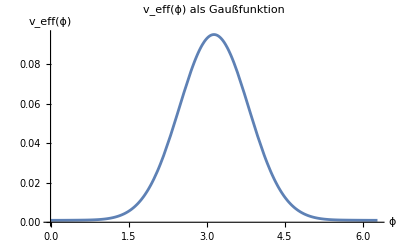

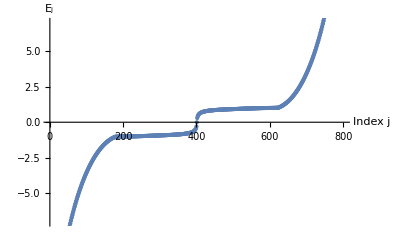

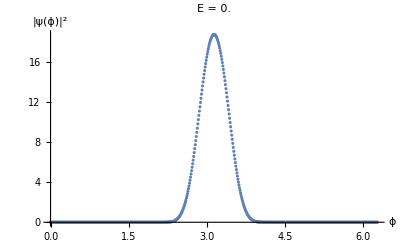

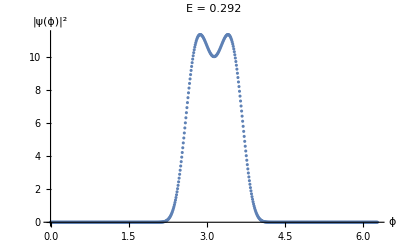

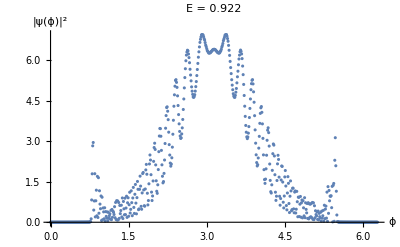

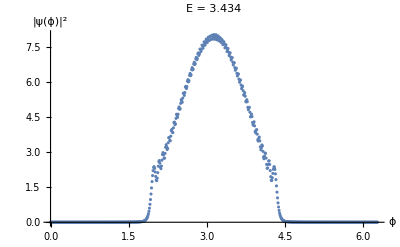

```mathematica
ϵvValues={1,0.026,0,0.0400369,0,0.0205556,0,0.00676676,0,0.00142828,0,0.000193296};
θVerschiebung=Pi;

v0Test=ϵvValues[[2]];
lValues=Range[1,Length[ϵvValues[[3;;]]]]
vlTest=0.5*ϵvValues[[3;;]]*(Exp[I*lValues/2 * ϕ]+Exp[-I*lValues/2 * ϕ])*Exp[I*lValues/2 * θVerschiebung]
Plot[Re[v0Test+Total[vlTest]],{ϕ,0,2 Pi},
PlotRange->{Automatic,{0,Automatic}}, PlotLabel->"v_eff(ϕ) als Gaußfunktion",AxesLabel->{"ϕ","v_eff(ϕ)"}]



{vals,vecs}=Eigensystem[Mv/.Thread[{ϵ0,v0,v1,v2,v3,v4,v5,v6,v7,v8,v9,v10}->ϵvValues]];
ListPlot[Sort[Re[vals]],AxesLabel->{"Index j","E_j"}]


PlotsvGauss03={};
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{Re[vals],vecs}],First]];
positionsv={401,402,500,700};(*{100,380,393,395,399,401,403,407,409,422,702};*)

For[i=1,i<=Length[positionsv],i++,
pos=positionsv[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1v=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2v=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψv=Conjugate[{ψ1v,ψ2v}].{ψ1v,ψ2v};
plot=ListPlot[
Table[{ϕ,Re[ψv]},{ϕ,0,2Pi,0.01}],
Ticks->{Automatic,None},
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]];
AppendTo[PlotsvGauss03,plot]
Print[plot]
]
(*GraphicsRow[PlotsvGauss03,ImageSize->Full]*)
```